```mathematica
space=0.025;
vp={3.2,0.2,0.8};
vv={0,0,1};
Dynamic[vp]
Dynamic[vv]
max=4.5
factor=2;
Dynamic[Show[
ParametricPlot3D[{Cos[2π t],Sin[2π t],t/factor},{t,0,max},Axes->False,Boxed->False,PlotStyle->Black,PlotRange->{Full,Full,{-4space/factor,(max+4space)/factor}}],
Table[
Graphics3D[{PointSize[Medium],Point[{Cos[2π t],Sin[2π t],t/factor}]}],
{t,max+space,max+3space,space}
],
Table[
Graphics3D[{PointSize[Medium],Point[{Cos[2π t],Sin[2π t],t/factor}]}],
{t,-space,-3space,-space}
],
ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]
]]
Export[FileNameJoin[{NotebookDirectory[],"covering_space.pdf"}],%]
Dynamic[Show[
ParametricPlot3D[{Cos[2π t],Sin[2π t],0},{t,0,2π},Axes->False,Boxed->False,PlotStyle->Black,PlotRange->{Full,Full,{-0.1,0.1}}],
ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]
]]
Export[FileNameJoin[{NotebookDirectory[],"circle.pdf"}],%]
```

4.5

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\covering_space.pdf

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\circle.pdf

```mathematica
Table[Table[(-1)^Subscript[s, i],{i,1,4}],Evaluate[Sequence@@Table[{Subscript[s, i],0,1},{i,1,4}]]]//.{a:({{__}..}..)}:>Union[a]
```

{{-1,-1,-1,-1},{-1,-1,-1,1},{-1,-1,1,-1},{-1,-1,1,1},{-1,1,-1,-1},{-1,1,-1,1},{-1,1,1,-1},{-1,1,1,1},{1,-1,-1,-1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,1,1},{1,1,-1,-1},{1,1,-1,1},{1,1,1,-1},{1,1,1,1}}

```mathematica
Sort[Tuples[{-1,1},2]]
```

{{-1,-1},{-1,1},{1,-1},{1,1}}

{(-1)^s_1,(-1)^s_2,(-1)^s_3,(-1)^s_4}

```mathematica
Nearest[Drop[Tuples[{-1,1},2],1],{-1,-1}]
```

{{-1,1},{1,-1}}

```mathematica
With[{count=3},BezierCurve[Join[{0,0,0},Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],z/count},{z,1,count}]]]
]
```

BezierCurve[{0,0,0,{-0.911428,0.614518,1/3},{0.245847,-0.669866,2/3},{-0.177489,0.0873092,1}}]

```mathematica
BetaDistribution[(m^2-m^3-m σ^2)/σ^2,((m^2-m^3-m σ^2)/σ^2)(1-m)/m]
```

BetaDistribution[(m^2-m^3-m σ^2)/σ^2,((1-m) (m^2-m^3-m σ^2))/(m σ^2)]

```mathematica
Tuples[{-1,1},2];
plane=Map[Join[#,{0}]&,{{-1,-1},{-1,1},{1,1},{1,-1}}];
ClearAll[MakeCurveFrom];
MakeCurveFrom[pt0_,0,ranges_:{}]:={};
MakeCurveFrom[pt0_,n_,ranges_:{{-1,1},{-1,1},{0,1}}]:=Join[{pt0},MakeCurveFrom[MapThread[
#1⟦1⟧+(#1⟦2⟧-#1⟦1⟧)RandomVariate[
With[{m=(#2-#1⟦1⟧)/(#1⟦2⟧-#1⟦1⟧),α=2},BetaDistribution[α,α(1-m)/m+0.1]]
]&,
{Take[ranges,Length[pt0]],pt0}
],
n-1,
ranges
]
];
Show[Evaluate[Graphics3D[Polygon[plane],Boxed->False]],
With[{countPt=3,countPath=10,countStartPt=10},Graphics3D[MapThread[
Function[{x0,y0,n},
{
ColorData["Rainbow"][n/countStartPt],
Table[
BezierCurve[Join[{{x0,y0,0},{x0,y0,1}},
Drop[MapIndexed[Join[#1,(#2-1)/(countPt-1)]&,MakeCurveFrom[{x0,y0},countPt]],1]
]
],
{i,1,countPath}]
}
],
{
RandomVariate[UniformDistribution[{-1,1}],countStartPt],
RandomVariate[UniformDistribution[{-1,1}],countStartPt],
Table[n,{n,1,countStartPt}]
}
]
]
]
]
```

-Graphics3D-

```mathematica
Tuples[{-1,1},2]
```

{{-1,-1},{-1,1},{1,-1},{1,1}}

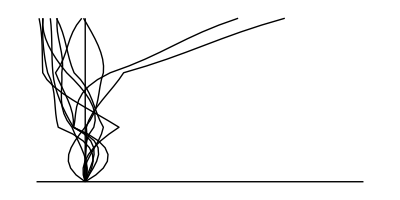

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I.pdf

-Graphics-

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I_1o2.pdf

-Graphics-

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I_1o3.pdf

-Graphics-

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I_2o3.pdf

-Graphics-

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I_1o4.pdf

-Graphics-

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X^I_3o4.pdf

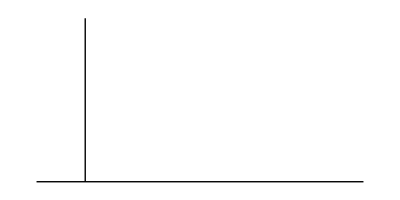

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X_to_X^I.pdf

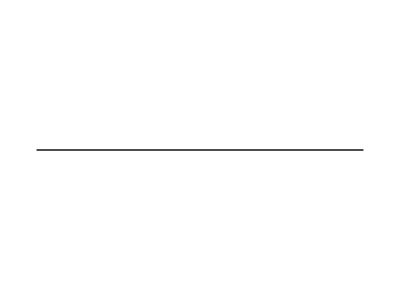

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X.pdf

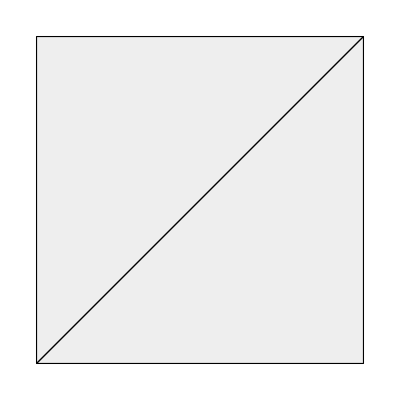

D:\Documents\Dropbox\MIT\2011-2012\18.904 - Seminar in Topology\Quillen Model Structures\path_object-X_x_X.pdf

```mathematica
Tuples[{-1,1},1];
line=Map[Join[#,{0}]&,%];
ClearAll[MakeCurveFrom];
MakeCurveFrom[pt0_,0,ranges_:{}]:={};
MakeCurveFrom[pt0_,n_,ranges_:{{-1,1},{0,1}}]:=Join[{pt0},MakeCurveFrom[MapThread[
#1⟦1⟧+(#1⟦2⟧-#1⟦1⟧)RandomVariate[
With[{m=(#2-#1⟦1⟧)/(#1⟦2⟧-#1⟦1⟧),α=5},BetaDistribution[α,α(1-m)/m+0.1]]
]&,
{Take[ranges,Length[pt0]],pt0}
],
n-1,
ranges
]
];
lines={};
colors={};
bcs={};
Show[Evaluate[Graphics[Line[line]]],
With[{countPt=10,countPath=10,countStartPt=1},Graphics[MapThread[
Function[{x0,n},
{
(
colors=Join[colors,{color=Black(*ColorData["Rainbow"][n/countStartPt]*)}];
color
),
(
lines=Join[
lines,
{{
color,
curline=Line[{{x0,0},{x0,1}}]
}}
];
curline
),
(bcs=Join[bcs,{bcscur=Table[
BezierCurve[Join[{{x0,0}(*,{x0,1}*)},
Drop[MapIndexed[Join[#1,(#2-1)/(countPt-1)]&,MakeCurveFrom[{x0},countPt]],1]
]
],
{i,1,countPath}]}];
bcscur)
}
],
{
RandomVariate[UniformDistribution[{-1,1}],countStartPt],
Table[n,{n,1,countStartPt}]
}
]
]
]
]
img=%;
Export[FileNameJoin[{NotebookDirectory[],"path_object-X^I.pdf"}],img]
CropToFraction[num_,den_]:=(
With[{cImg=ImageCrop[img,{Full,(1-num/den)ImageDimensions[img]⟦2⟧},Top]},
Print[Show[cImg]];
Print[Export[FileNameJoin[{NotebookDirectory[],"path_object-X^I_"<>ToString[num]<>"o"<>ToString[den]<>".pdf"}],cImg]];
]
);
CropToFraction[x_Rational]:=CropToFraction[Numerator[x],Denominator[x]];
CropToFraction[1/2]
CropToFraction[1/3]
CropToFraction[2/3]
CropToFraction[1/4]
CropToFraction[3/4]
Show[Evaluate[Graphics[Line[line]]],Map[Graphics,lines]]
Export[FileNameJoin[{NotebookDirectory[],"path_object-X_to_X^I.pdf"}],%]
Show[Evaluate[Graphics[Line[line]]]]
Export[FileNameJoin[{NotebookDirectory[],"path_object-X.pdf"}],%]
Show[Graphics[{Lighter@Lighter@Lighter[Lighter[Lighter[Gray]]],EdgeForm[{Black}],Polygon[{{-1,-1},{-1,1},{1,1},{1,-1}}]}],Graphics[{Thick,Line[{{-1,-1},{1,1}}]}](*,
Graphics[lines/.Line[{{x_,_},___}]:>{PointSize[Large],Point[{x,x}]}]*)
(*,Graphics[MapThread[{#1,#2}&,
{colors,
bcs/.BezierCurve[{{x0_,_},___,{xf_,_}}]:>Point[{x0,xf}]}
]]*)]
Export[FileNameJoin[{NotebookDirectory[],"path_object-X_x_X.pdf"}],%]
```

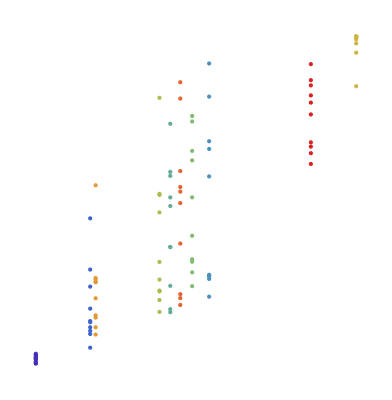

```mathematica
Show[Graphics[MapThread[{#1,#2}&,
{colors,
bcs/.BezierCurve[{{x0_,_},___,{xf_,_}}]:>Point[{x0,xf}]}
]]]
```

```mathematica
Graphics[lines/.Line[{{x_,_},___}]:>{PointSize[Large],Point[{x,x}]}]
```

-Graphics-